## Modelo de Brendel Borman

```mathematica
faddeeva=ResourceFunction["FaddeevaW"];
```

```mathematica
brendelBormanModel[w0_,sigma_,w_,g_,wp_,f_]:=Module[{a1,a2,a,b,w1,w2,xi,eps},
a1=w/(Sqrt[2])*Sqrt[Sqrt[1+(g/w)^2]+1];
a2=w/(Sqrt[2])*Sqrt[Sqrt[1+(g/w)^2]-1];
a=a1+I*a2;
b=(I*f*wp^2)/(2*Sqrt[2]*a*sigma);
w1=faddeeva[(a-w0)/(Sqrt[2]*sigma)];
w2=faddeeva[(a+w0)/(Sqrt[2]*sigma)];
xi=b*(w1+w2);
eps=1+xi]
```

```mathematica
ϵDrude[w_,wp_,g0_,f0_]:=1-((f0*wp^2)/((w)(w+I * g0)));(*recibe en eV*)
```

```mathematica
epsTotBB[w_,wp_,g_,f_,w0_,sigma_]:=ϵDrude[w,wp,g[[1]],f[[1]]]+Sum[brendelBormanModel[w0[[i]],sigma[[i]],w,g[[i]],wp,f[[i]]],{i,2,Length[w0]}]
```

```mathematica
w0AuBB={0,0.2626,2.673,3.933,3.008,9.278,4.839};
fAuBB={0.4069,0.04902,0.008967,0.08671,0.07188,1.545,0.4499};
gAuBB={0.003061,0.1127,0.02089,0.001,0.001,0.001901,0.6266};
sigmaAuBB={0,0.05877,1.561,5.146,0.3832,1.854,1.107};
wpAuBB=9.03;
```

```mathematica
epsTotBB[5,wpAuBB,gAuBB,fAuBB,w0AuBB,sigmaAuBB]
```

6.58782+2.36632 ⅈ

```mathematica
holaBB=Table[{w,-Re[epsTotBB[w,wpAuBB,gAuBB,fAuBB,w0AuBB,sigmaAuBB]]},{w,0.5,7,0.01}];
hola1BB=Table[{w,Im[epsTotBB[w,wpAuBB,gAuBB,fAuBB,w0AuBB,sigmaAuBB]]},{w,0.5,7,0.01}];
```

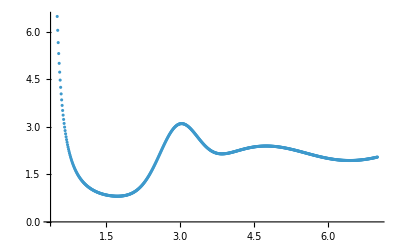

```mathematica
ListPlot[{hola1BB},PlotRange->All]
```